## HDR Tone-Mapping This document defines and compares a variety of HDR to LDR tone-mapping operators. Common tone-mapping operators

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Unreal Engine *)
unrealOp[x_,offset_,scale_] := x / (x + offset) * scale
unreal[x_] := unrealOp[x, 0.187,1.035]
linearUnreal[x_] := unrealOp[x, 0.187,1.035]^2.2

(* Reinhard *)
Reinhard[x_] := (x / (1 + x))^(1/2.2)
linearReinhard[x_] := x / (1 + x)

(* Uncharted 2 (filmic) *)
uncharted2op[x_] := Module[
{a=0.15, b=0.50, c= 0.1, d=0.2, e=0.02, f=0.3},
((x*(a*x+c*b)+d*e)/(x*(a*x+b)+d*f))-e/f
]
uncharted2[x_]:=(uncharted2op[2*x]/uncharted2op[11.2])^(1/2.2)
linearUncharted2[x_]:=uncharted2op[2*x]/uncharted2op[11.2]

(* Filmic ALU *)
filmicALU[x_]:=Module[
{c=Max[0, x - 0.004]},
(c*(6.2*c+0.5))/(c*(6.2*c+1.7)+0.06)
]
linearFilmicALU[x_]:=filmicALU[x]^2.2

(* ACES operator, for LDR and HDR *)
ACESop[x_,a_, b_, c_, d_, e_]:= (x*(a*x+b))/(x*(c*x+d)+e)

(* ACES sRGB *)
ACES[x_]:=linearACES[x]^(1/2.2)
linearACES[x_] := Clip[ACESop[x, 2.51, 0.03, 2.43, 0.59, 0.14],{0,1}]

(* ACES Rec2020 1,000 nits *)
linearACESRec20201k[x_]:= ACESop[x, 15.8, 2.12, 1.2, 5.92, 1.9]

(* Siragusano-Smith *)
linearSiragusanoSmithImpl[x_,contrast_,middleGreyIn_,middleGreyOut_,ev_]:=Block[
{
radiometricMax=2.0^ev*middleGreyIn,
inputScale=((radiometricMax*middleGreyIn)*(middleGreyOut^(1.0/contrast)-1.0))/(middleGreyIn-(radiometricMax*middleGreyOut^(1.0/contrast))),
outputScale=(radiometricMax/(radiometricMax+inputScale))^-contrast
},
outputScale*(x/(x+inputScale))^contrast
]
linearSiragusanoSmith[x_]:=linearSiragusanoSmithImpl[x,3.33,0.18,0.281,5.5]
SiragusanoSmith[x_]:=linearSiragusanoSmith[x]^(1/2.2)

(* Linear *)
noTonemap[x_]:=x
linearNoTonemap[x_]:=x^(1.0/2.2)

toneMapOperators := {
ACES,
unreal,
uncharted2,
filmicALU,
Reinhard,
SiragusanoSmith,
noTonemap

}
linearToneMapOperators := {
linearACES,
linearUnreal,
linearUncharted2,
linearFilmicALU,
linearReinhard,
linearSiragusanoSmith,
linearNoTonemap
}
operatorNames := { "ACES", "Unreal", "Uncharted 2", "FilmicALU", "Reinhard","Siragusano-Smith", "None"}

linearACESToneMapOperators := {
linearACES,
linearACESRec20201k
}
acesOperatorNames := { "ACES", "ACES Rec.2020 1k" }
```

## Generic tone-mapping operator The generic tone-mapping operator can be customized using the following parameters:

## hdrMax maximum input HDR value that will be mapped to 1.0 contrast controls the contrast of the curve (the toe) shoulder controls the shoulder of the curve midIn input middle gray (0.18 for 18% gray for instance) midOut output middle gray

```mathematica
(* Note: the b and c parameters can be pre-computed on the CPU side *)
generic[x_,hdrMax_,contrast_,shoulder_,midIn_,midOut_]:=
Module[
{b,c},
b:=(-midIn^contrast+(hdrMax^contrast)*midOut)/(((hdrMax^contrast)^shoulder-(midIn^contrast)^shoulder)*midOut);
c:=(((hdrMax^contrast)^shoulder)*midIn^contrast-hdrMax^contrast*((midIn^contrast)^shoulder)*midOut)/(((hdrMax^contrast)^shoulder-(midIn^contrast)^shoulder)*midOut);
Clip[(x^contrast)/((x^contrast)^shoulder*b+c),{0,1}]
]
```

```mathematica
(* The default parameters match the ACES tone-mapping operator *)
Manipulate[
     LogLinearPlot[
   (* We plot the ACES operator for reference *) 
   {generic[x,hdrMax,contrast,shoulder,midIn,midOut],linearACES[x]}, {x, 0.01, hdrMax*2},
    ImageSize->Large
  ],
   {{hdrMax, 8.0}, 1.0, 64.0,Appearance->"Labeled"},
   {{contrast, 1.6}, 0.2, 4.0,Appearance->"Labeled"},
   {{shoulder, 0.977}, 0.8, 1.1,Appearance->"Labeled"},
   {{midIn, 0.18}, 0.01, 1.0,Appearance->"Labeled"},
   {{midOut, 0.267}, 0.01, 1.0,Appearance->"Labeled"}
]
```

```mathematica
Manipulate[
     LogLinearPlot[
   (* We plot the ACES operator for reference *) 
   {linearSiragusanoSmithImpl[x,contrast,midIn,midOut,hdrMax],linearACES[x]}, {x, 0.001, hdrMax*2.5},
    ImageSize->Large
  ],
   {{hdrMax,5.5}, 1.0, 16.0,Appearance->"Labeled"},
   {{contrast, 1.2}, 0.2, 8.0,Appearance->"Labeled"},
   {{midIn, 0.18}, 0.01, 1.0,Appearance->"Labeled"},
   {{midOut, 0.18}, 0.01, 1.0,Appearance->"Labeled"}
]
```

## Operators comparison

#### Curve plots (linear)

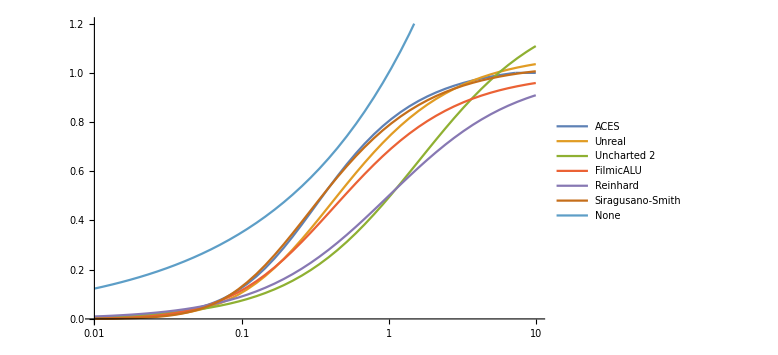

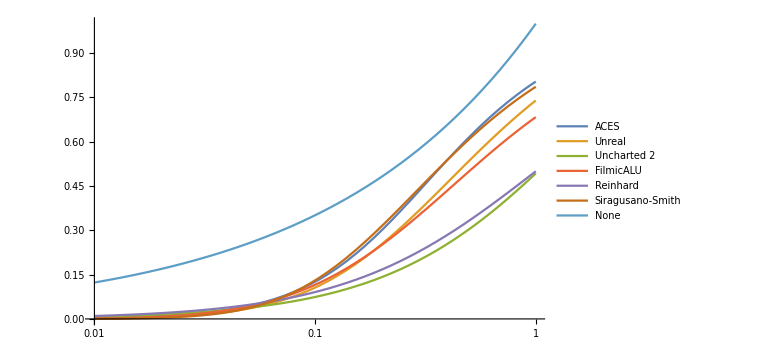

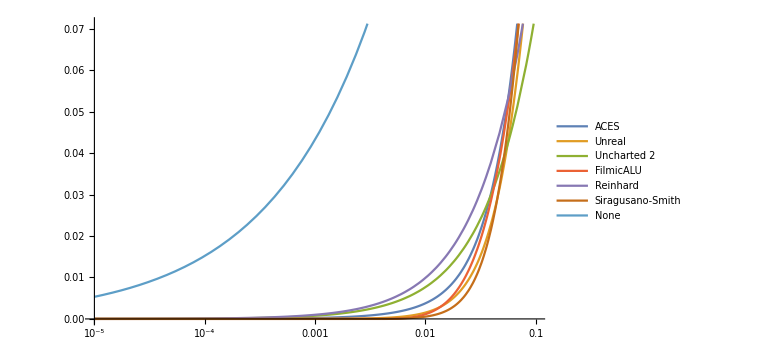

```mathematica
plotFns=#[x]&/@linearToneMapOperators;
LogLinearPlot[plotFns, {x, 0.01, 10}, ImageSize->Large, PlotRange->{0, 1.2}, PlotLegends->operatorNames]
LogLinearPlot[plotFns, {x,0.01, 1}, ImageSize->Large, PlotRange->Automatic, PlotLegends->operatorNames]
LogLinearPlot[plotFns, {x, 0.00001, 0.1}, ImageSize->Large, PlotRange->Automatic, PlotLegends->operatorNames]
```

#### Curve plots (sRGB)

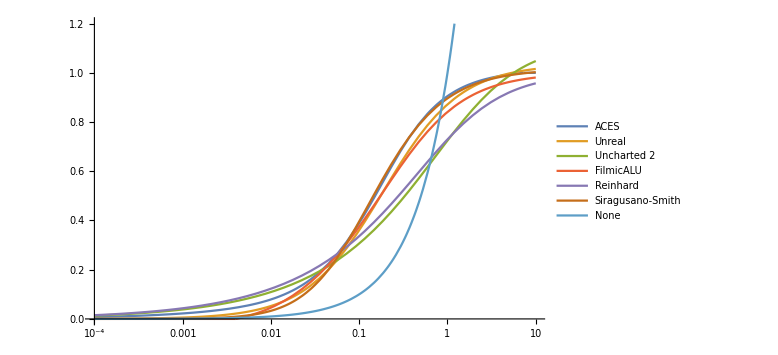

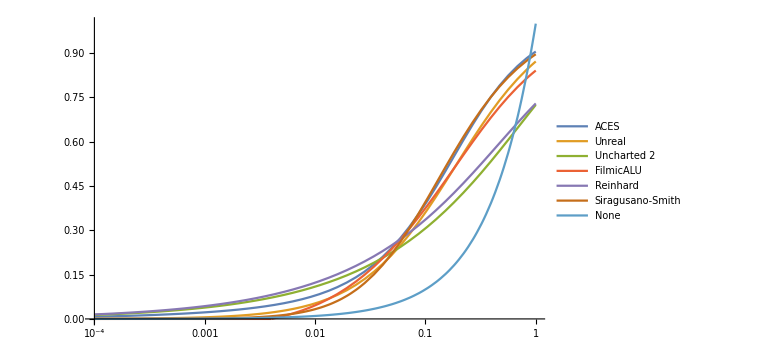

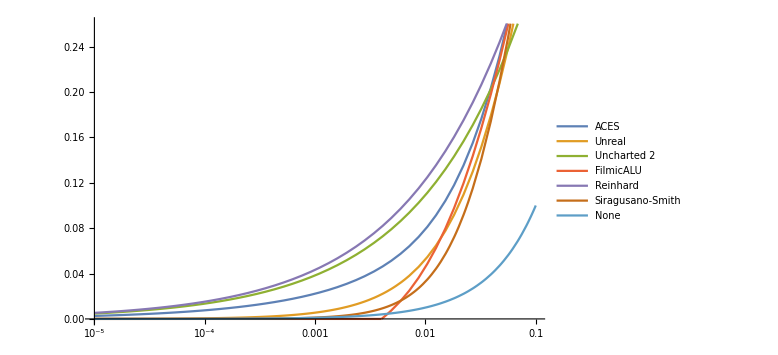

```mathematica
plotFns=#[x]&/@toneMapOperators;
LogLinearPlot[plotFns, {x, 0.0001, 10}, ImageSize->Large, PlotRange->{0, 1.2}, PlotLegends->operatorNames]
LogLinearPlot[plotFns, {x, 0.0001, 1}, ImageSize->Large, PlotRange->Automatic, PlotLegends->operatorNames]
LogLinearPlot[plotFns, {x, 0.00001, 0.1}, ImageSize->Large, PlotRange->Automatic, PlotLegends->operatorNames]
```

#### Curve plots (ACES LDR and HDR)

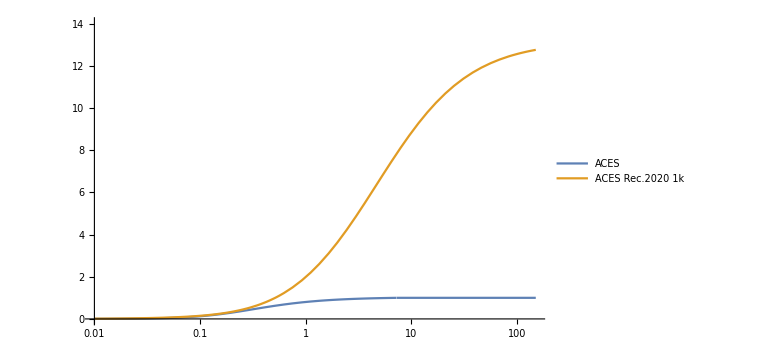

```mathematica
plotFns=#[x]&/@linearACESToneMapOperators;
LogLinearPlot[plotFns, {x, 0.01, 150}, ImageSize->Large, PlotRange->{0, 14}, PlotLegends->acesOperatorNames]
```